## EDS spectra plotter

This notebook simply plots EDS spectra imported from .csv data and labels peaks with hard-coded tabulated data. EDS maps are shown for reference.

June 2019

```mathematica
img062019=Import["E:\\4D STEM project\\TEM images\\15 June 19\\zoom all.tif"]
```

-Graphics-

```mathematica
data062019=Import["E:\\4D STEM project\\TEM images\\15 June 19\\omg amazing zoom EDS spectrum data.csv","CSV"]⟦26;;-1,2;;3⟧;
```

```mathematica
data062019divided={data062019⟦48;;-1,1⟧,data062019⟦48;;-1,2⟧/135.012}ᵀ;
```

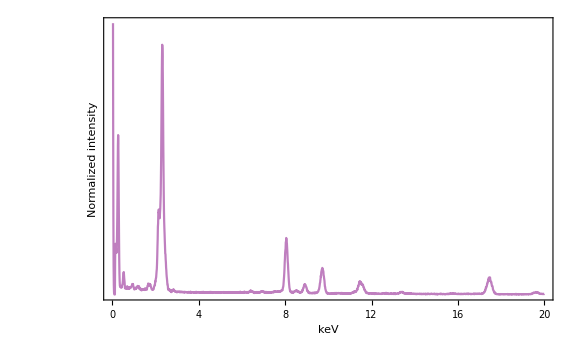

```mathematica
plot062019=ListPlot[data062019divided,Joined->True,PlotRange->{{0,20},{0,65}},Frame->True,FrameLabel->{"keV","Normalized intensity"},RotateLabel->True,ImageSize->Large,LabelStyle->{16,Black},PlotStyle->{Purple,Opacity[0.5]},FrameTicks->{{None,None},{Range[0,20,2],None}}]
```

July 2019

```mathematica
img072019=Import["E:\\4D STEM project\\TEM images\\16 July 19\\2_EDS.png"]
```

-Graphics-

Need to export EDS data for analysis here.

November 2019 - area 2

```mathematica
img112019a2=Import["E:\\4D STEM project\\TEM images\\20 November 19\\EDS\\area 2_all.png"]
```

-Graphics-

```mathematica
data112019a2=Import["E:\\4D STEM project\\TEM images\\20 November 19\\EDS\\area 2_EDS spectrum data.csv","CSV"]⟦26;;-1,2;;3⟧;
```

```mathematica
data112019a2divided={data112019a2⟦48;;-1,1⟧,data112019a2⟦48;;-1,2⟧/150.412}ᵀ;
```

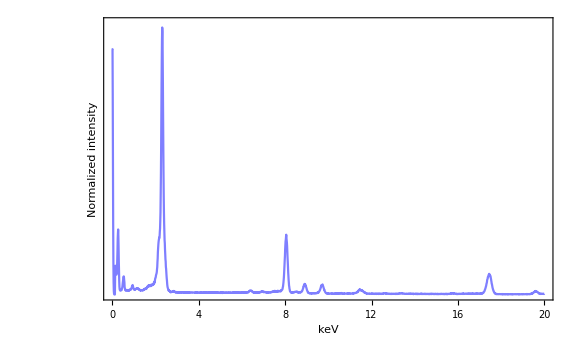

```mathematica
plot112019a2=ListPlot[data112019a2divided,Joined->True,PlotRange->{{0,20},{0,145}},Frame->True,FrameLabel->{"keV","Normalized intensity"},RotateLabel->True,ImageSize->Large,LabelStyle->{16,Black},PlotStyle->{Blue,Opacity[0.5]},FrameTicks->{{None,None},{Range[0,20,2],None}}]
```

November 2019 - area 4

```mathematica
img112019=Import["E:\\4D STEM project\\TEM images\\20 November 19\\EDS\\area 4_all.png"]
```

-Graphics-

```mathematica
data112019=Import["E:\\4D STEM project\\TEM images\\20 November 19\\EDS\\area 4_EDS spectrum data.csv","CSV"]⟦26;;-1,2;;3⟧;
```

```mathematica
data112019divided={data112019⟦48;;-1,1⟧,data112019⟦48;;-1,2⟧/238.547}ᵀ;
```

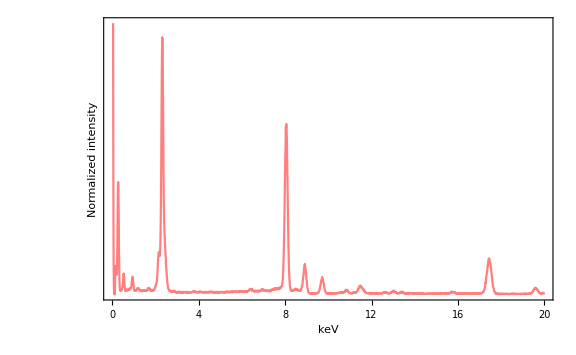

```mathematica
plot112019=ListPlot[data112019divided,Joined->True,PlotRange->{{0,20},{0,47}},Frame->True,FrameLabel->{"keV","Normalized intensity"},RotateLabel->True,ImageSize->Large,LabelStyle->{16,Black},PlotStyle->{Red,Opacity[0.5]},FrameTicks->{{None,None},{Range[0,20,2],None}}]
```

## Let’s look at them together:

```mathematica
moLines=ListLinePlot[{{{17.481,0},{17.441,15}},{{19.606,0},{19.606,5}},{{2.293,0},{2.293,80}}},PlotStyle->{{RGBColor[0,1,1],Opacity[0.7]},{RGBColor[0,1,1],Opacity[0.7]},{RGBColor[0,1,1],Opacity[0.7]}}];
auLines=ListLinePlot[{{{9.712,0},{9.712,10}},{{11.443,0},{11.443,6}},{{2.12,0},{2.12,30}}},PlotStyle->{{RGBColor[0,1,0],Opacity[0.7]},{RGBColor[0,1,0],Opacity[0.7]},{RGBColor[0.,1.,0],Opacity[0.7]}}];
cuLines=ListLinePlot[{{{8.046,0},{8.046,35}},{{8.904,0},{8.904,10}},{{0.93,0},{0.93,5}}},PlotStyle->{{Red,Opacity[0.7]},{Red,Opacity[0.7]},{Red,Opacity[0.7]}}];
```

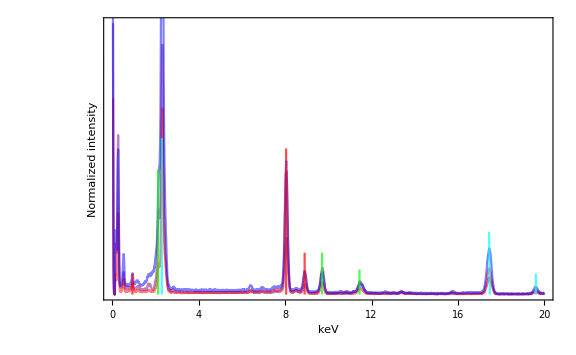

```mathematica
Show[{plot062019,plot112019,plot112019a2,moLines,auLines,cuLines}]
```